# Materials 15 1 Feb 2020

```mathematica
ClearAll
```

ClearAll

```mathematica
<<Notation` 
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
```

### ---

### Need to define these things: set StandardForm to TraditionalForm for TeXForm to work with subscripts. Then run the updateSubscriptTraditionalForm[] command before copying the latex expressions.

```mathematica
SetAttributes[standardToTraditionalBoxes,HoldAllComplete]
standardToTraditionalBoxes[boxes_]:=Function[expr,MakeBoxes[expr,TraditionalForm],HoldAllComplete]@@MakeExpression[boxes,StandardForm]
```

```mathematica
addSubscriptTraditionalForm[Verbatim[HoldPattern][Verbatim[Condition][Notation`NotationMakeBoxes[sym_Symbol,StandardForm],_]]:>SubscriptBox[x_,y_]]:=(sym/:MakeBoxes[sym,TraditionalForm]=SubscriptBox[standardToTraditionalBoxes[x],standardToTraditionalBoxes[y]])
```

```mathematica
updateSubscriptTraditionalForm[]:=Scan[addSubscriptTraditionalForm,DownValues[Notation`NotationMakeBoxes]]
```

```mathematica
updateSubscriptTraditionalForm[]
```

Now load the ToMatlab package.

```mathematica
<<ToMatlab`
```

-----------------------------------------

## Woodford’s optimal noninertial plan (oni). (See Notes 1 Feb 2020.)

```mathematica
fp=.; fx=.; fi=.;
```

```mathematica
gp=.; gx=.; gi=.;
```

```mathematica
κ =.; β =.; Subscript[ρ, u]=.;
```

```mathematica
Subscript[ρ, r]=.; σ =.;
```

```mathematica
Subscript[λ, x]=.; Subscript[λ, i]=.;
```

```mathematica
C1 = -fp + κ*fx + β*fp*Subscript[ρ, u] + 1
```

1-fp+fx κ+fp β ρ_u

```mathematica
C2 = -gp +κ*gx + β*gp*Subscript[ρ, r]
```

-gp+gx κ+gp β ρ_r

```mathematica
C3 = -fx + fx*Subscript[ρ, u]-σ*fi + σ*fp*Subscript[ρ, u]
```

-fx+fx ρ_u-fi σ+fp ρ_u σ

```mathematica
C4 = -gx + gx*Subscript[ρ, r]-σ*gi + σ*gp*Subscript[ρ, r] + σ
```

-gx+gx ρ_r+σ-gi σ+gp ρ_r σ

#### First the f-coefficients

```mathematica
Solve[{C1==0},fx]
```

{{fx→(-1+fp-fp β ρ_u)/κ}}

```mathematica
fxs = (-1+fp-fp β Subscript[ρ, u])/κ;
```

```mathematica
C3p = C3 /. {fx -> fxs};
```

```mathematica
Solve[C3p==0,fi]
```

{{fi→(1-fp-ρ_u+fp ρ_u+fp β ρ_u-fp β ρ_u^2+fp κ ρ_u σ)/(κ σ)}}

```mathematica
fis = (1-fp-Subscript[ρ, u]+fp Subscript[ρ, u]+fp β Subscript[ρ, u]-fp β Subscript[ρ, u]^2+fp κ Subscript[ρ, u] σ)/(κ σ);
```

```mathematica
Lstabu = fp^2 + Subscript[λ, x]*fx^2 +Subscript[λ, i]*fi^2
```

fp^2+fi^2 λ_i+fx^2 λ_x

```mathematica
Lstabu1 = Lstabu /.{fx -> fxs, fi -> fis}
```

fp^2+(λ_x (-1+fp-fp β ρ_u)^2)/κ^2+(λ_i (1-fp-ρ_u+fp ρ_u+fp β ρ_u-fp β ρ_u^2+fp κ ρ_u σ)^2)/(κ^2 σ^2)

```mathematica
FOCu = D[Lstabu1,fp]
```

2 fp+(2 λ_x (1-β ρ_u) (-1+fp-fp β ρ_u))/κ^2+(2 λ_i (-1+ρ_u+β ρ_u-β ρ_u^2+κ ρ_u σ) (1-fp-ρ_u+fp ρ_u+fp β ρ_u-fp β ρ_u^2+fp κ ρ_u σ))/(κ^2 σ^2)

```mathematica
Solve[FOCu==0,fp]
```

{{fp→(λ_i-2 λ_i ρ_u-β λ_i ρ_u+λ_i ρ_u^2+2 β λ_i ρ_u^2-β λ_i ρ_u^3-κ λ_i ρ_u σ+κ λ_i ρ_u^2 σ+λ_x σ^2-β λ_x ρ_u σ^2)/(λ_i-2 λ_i ρ_u-2 β λ_i ρ_u+λ_i ρ_u^2+4 β λ_i ρ_u^2+β^2 λ_i ρ_u^2-2 β λ_i ρ_u^3-2 β^2 λ_i ρ_u^3+β^2 λ_i ρ_u^4-2 κ λ_i ρ_u σ+2 κ λ_i ρ_u^2 σ+2 β κ λ_i ρ_u^2 σ-2 β κ λ_i ρ_u^3 σ+κ^2 σ^2+λ_x σ^2-2 β λ_x ρ_u σ^2+κ^2 λ_i ρ_u^2 σ^2+β^2 λ_x ρ_u^2 σ^2)}}

```mathematica
fponi =(Subscript[λ, i]-2 Subscript[λ, i] Subscript[ρ, u]-β Subscript[λ, i] Subscript[ρ, u]+Subscript[λ, i] Subscript[ρ, u]^2+2 β Subscript[λ, i] Subscript[ρ, u]^2-β Subscript[λ, i] Subscript[ρ, u]^3-κ Subscript[λ, i] Subscript[ρ, u] σ+κ Subscript[λ, i] Subscript[ρ, u]^2 σ+Subscript[λ, x] σ^2-β Subscript[λ, x] Subscript[ρ, u] σ^2)/(Subscript[λ, i]-2 Subscript[λ, i] Subscript[ρ, u]-2 β Subscript[λ, i] Subscript[ρ, u]+Subscript[λ, i] Subscript[ρ, u]^2+4 β Subscript[λ, i] Subscript[ρ, u]^2+β^2 Subscript[λ, i] Subscript[ρ, u]^2-2 β Subscript[λ, i] Subscript[ρ, u]^3-2 β^2 Subscript[λ, i] Subscript[ρ, u]^3+β^2 Subscript[λ, i] Subscript[ρ, u]^4-2 κ Subscript[λ, i] Subscript[ρ, u] σ+2 κ Subscript[λ, i] Subscript[ρ, u]^2 σ+2 β κ Subscript[λ, i] Subscript[ρ, u]^2 σ-2 β κ Subscript[λ, i] Subscript[ρ, u]^3 σ+κ^2 σ^2+Subscript[λ, x] σ^2-2 β Subscript[λ, x] Subscript[ρ, u] σ^2+κ^2 Subscript[λ, i] Subscript[ρ, u]^2 σ^2+β^2 Subscript[λ, x] Subscript[ρ, u]^2 σ^2);
```

```mathematica
FullSimplify[fponi]
```

(λ_x (1-β ρ_u) σ^2+λ_i (-1+ρ_u) (-1+ρ_u (1+β-β ρ_u+κ σ)))/((κ^2+λ_x (-1+β ρ_u)^2) σ^2+λ_i (-1+ρ_u (1+β-β ρ_u+κ σ))^2)

```mathematica
fxoni = fxs /. {fp -> fponi};
```

```mathematica
FullSimplify[fxoni]
```

-(σ (κ σ+λ_i ρ_u (-1+ρ_u (1+β-β ρ_u+κ σ))))/((κ^2+λ_x (-1+β ρ_u)^2) σ^2+λ_i (-1+ρ_u (1+β-β ρ_u+κ σ))^2)

```mathematica
fioni = fis /. {fp-> fponi};
```

```mathematica
FullSimplify[fioni]
```

-(σ (κ (-1+ρ_u)+λ_x ρ_u (-1+β ρ_u) σ))/((κ^2+λ_x (-1+β ρ_u)^2) σ^2+λ_i (-1+ρ_u (1+β-β ρ_u+κ σ))^2)

#### Now the g-coefficients

```mathematica
Solve[{C2==0},gx]
```

{{gx→(gp-gp β ρ_r)/κ}}

```mathematica
gxs = (gp-gp β Subscript[ρ, r])/κ;
```

```mathematica
C4p = C4 /. {gx -> gxs};
```

```mathematica
Solve[C4p==0,gi]
```

{{gi→(-gp+gp ρ_r+gp β ρ_r-gp β ρ_r^2+κ σ+gp κ ρ_r σ)/(κ σ)}}

```mathematica
gis = (-gp+gp Subscript[ρ, r]+gp β Subscript[ρ, r]-gp β Subscript[ρ, r]^2+κ σ+gp κ Subscript[ρ, r] σ)/(κ σ);
```

```mathematica
Lstabr = gp^2 + Subscript[λ, x]*gx^2 +Subscript[λ, i]*gi^2
```

gp^2+gi^2 λ_i+gx^2 λ_x

```mathematica
Lstabr1 = Lstabr /.{gx -> gxs, gi -> gis}
```

gp^2+(λ_x (gp-gp β ρ_r)^2)/κ^2+(λ_i (-gp+gp ρ_r+gp β ρ_r-gp β ρ_r^2+κ σ+gp κ ρ_r σ)^2)/(κ^2 σ^2)

```mathematica
FOCr = D[Lstabr1,gp]
```

2 gp+(2 λ_x (1-β ρ_r) (gp-gp β ρ_r))/κ^2+(2 λ_i (-1+ρ_r+β ρ_r-β ρ_r^2+κ ρ_r σ) (-gp+gp ρ_r+gp β ρ_r-gp β ρ_r^2+κ σ+gp κ ρ_r σ))/(κ^2 σ^2)

```mathematica
Solve[FOCr==0,gp]
```

{{gp→-((κ λ_i σ (-1+ρ_r+β ρ_r-β ρ_r^2+κ ρ_r σ))/(λ_i-2 λ_i ρ_r-2 β λ_i ρ_r+λ_i ρ_r^2+4 β λ_i ρ_r^2+β^2 λ_i ρ_r^2-2 β λ_i ρ_r^3-2 β^2 λ_i ρ_r^3+β^2 λ_i ρ_r^4-2 κ λ_i ρ_r σ+2 κ λ_i ρ_r^2 σ+2 β κ λ_i ρ_r^2 σ-2 β κ λ_i ρ_r^3 σ+κ^2 σ^2+λ_x σ^2-2 β λ_x ρ_r σ^2+κ^2 λ_i ρ_r^2 σ^2+β^2 λ_x ρ_r^2 σ^2))}}

```mathematica
gponi = -((κ Subscript[λ, i] σ (-1+Subscript[ρ, r]+β Subscript[ρ, r]-β Subscript[ρ, r]^2+κ Subscript[ρ, r] σ))/(Subscript[λ, i]-2 Subscript[λ, i] Subscript[ρ, r]-2 β Subscript[λ, i] Subscript[ρ, r]+Subscript[λ, i] Subscript[ρ, r]^2+4 β Subscript[λ, i] Subscript[ρ, r]^2+β^2 Subscript[λ, i] Subscript[ρ, r]^2-2 β Subscript[λ, i] Subscript[ρ, r]^3-2 β^2 Subscript[λ, i] Subscript[ρ, r]^3+β^2 Subscript[λ, i] Subscript[ρ, r]^4-2 κ Subscript[λ, i] Subscript[ρ, r] σ+2 κ Subscript[λ, i] Subscript[ρ, r]^2 σ+2 β κ Subscript[λ, i] Subscript[ρ, r]^2 σ-2 β κ Subscript[λ, i] Subscript[ρ, r]^3 σ+κ^2 σ^2+Subscript[λ, x] σ^2-2 β Subscript[λ, x] Subscript[ρ, r] σ^2+κ^2 Subscript[λ, i] Subscript[ρ, r]^2 σ^2+β^2 Subscript[λ, x] Subscript[ρ, r]^2 σ^2));
```

```mathematica
FullSimplify[gponi]
```

-(κ λ_i σ (-1+ρ_r (1+β-β ρ_r+κ σ)))/((κ^2+λ_x (-1+β ρ_r)^2) σ^2+λ_i (-1+ρ_r (1+β-β ρ_r+κ σ))^2)

```mathematica
gxoni = gxs /.{gp-> gponi};
```

```mathematica
FullSimplify[gxoni]
```

-(λ_i (-1+β ρ_r) σ (1+β ρ_r^2-ρ_r (1+β+κ σ)))/((κ^2+λ_x (-1+β ρ_r)^2) σ^2+λ_i (-1+ρ_r (1+β-β ρ_r+κ σ))^2)

```mathematica
gioni = gis /. {gp->  gponi};
```

```mathematica
FullSimplify[gioni]
```

((κ^2+λ_x (-1+β ρ_r)^2) σ^2)/((κ^2+λ_x (-1+β ρ_r)^2) σ^2+λ_i (-1+ρ_r (1+β-β ρ_r+κ σ))^2)

Just check that the denom is really right, in particular the part under the square after λ_i:

```mathematica
Expand[-1+Subscript[ρ, r] (1+β-β Subscript[ρ, r]+κ σ)]
```

-1+ρ_r+β ρ_r-β ρ_r^2+κ ρ_r σ

```mathematica
Expand[(1-Subscript[ρ, r])*(1-β*Subscript[ρ, r])-Subscript[ρ, r]*κ*σ]
```

1-ρ_r-β ρ_r+β ρ_r^2-κ ρ_r σ

Ok, they are the same!

### Optimal Taylor rule coefficients

```mathematica
Subscript[ϕ, p]=.; Subscript[ϕ, x]=.;
```

```mathematica
T1 = Subscript[ϕ, p]*fp + Subscript[ϕ, x]*fx - fi;
```

```mathematica
T2 = Subscript[ϕ, p]*gp + Subscript[ϕ, x]*gx - gi;
```

```mathematica
T1p = T1 /.{fp -> fponi, fx-> fxoni, fi -> fioni};
```

```mathematica
T2p = T2 /.{gp -> gponi, gx-> gxoni, gi -> gioni};
```

```mathematica
FullSimplify[Solve[{T1p==0, T2p==0}, {Subscript[ϕ, p],Subscript[ϕ, x]}]]
```

{{ϕ_p→(σ (λ_i λ_x (-1+β ρ_r)^2 (ρ_r-ρ_u) ρ_u (-1+β ρ_u) σ-κ^2 λ_i (-1+ρ_u) (-ρ_r+β ρ_r^2+ρ_u (-1+β ρ_u)) σ+κ^3 (1+λ_i ρ_u^2) σ^2+κ (-1+β ρ_r) (λ_i (-1+ρ_r) (-1+β ρ_r) (-1+ρ_u)+λ_x (-1+β ρ_r+λ_i (ρ_r-ρ_u) ρ_u) σ^2)))/(λ_i (1+β ρ_r^2-ρ_r (1+β+κ σ)) ((κ^2+λ_x (-1+β ρ_r) (-1+β ρ_u)) σ^2+λ_i (1+β ρ_r (-1+ρ_u)-ρ_u (1+κ σ)) (1+β ρ_u^2-ρ_u (1+β+κ σ)))),ϕ_x→-((σ (λ_x (κ^2+λ_x (-1+β ρ_r)^2) (-1+β ρ_u) σ^2+κ^2 λ_i (ρ_r-ρ_u) (-1+ρ_u) (1-β (-1+ρ_r+ρ_u)+κ σ)+λ_i λ_x ((-1+β ρ_r)^2 (-1+ρ_u)^2 (-1+β ρ_u)-κ (-1+β ρ_r) ρ_u (2-(1+β) ρ_u+ρ_r (-1+β (-1+2 ρ_u))) σ+κ^2 ρ_r ρ_u (-1+β ρ_u) σ^2)))/(λ_i (1+β ρ_r^2-ρ_r (1+β+κ σ)) ((κ^2+λ_x (-1+β ρ_r) (-1+β ρ_u)) σ^2+λ_i (1+β ρ_r (-1+ρ_u)-ρ_u (1+κ σ)) (1+β ρ_u^2-ρ_u (1+β+κ σ)))))}}

```mathematica
phipiopt = (σ (Subscript[λ, i] Subscript[λ, x] (-1+β Subscript[ρ, r])^2 (Subscript[ρ, r]-Subscript[ρ, u]) Subscript[ρ, u] (-1+β Subscript[ρ, u]) σ-κ^2 Subscript[λ, i] (-1+Subscript[ρ, u]) (-Subscript[ρ, r]+β Subscript[ρ, r]^2+Subscript[ρ, u] (-1+β Subscript[ρ, u])) σ+κ^3 (1+Subscript[λ, i] Subscript[ρ, u]^2) σ^2+κ (-1+β Subscript[ρ, r]) (Subscript[λ, i] (-1+Subscript[ρ, r]) (-1+β Subscript[ρ, r]) (-1+Subscript[ρ, u])+Subscript[λ, x] (-1+β Subscript[ρ, r]+Subscript[λ, i] (Subscript[ρ, r]-Subscript[ρ, u]) Subscript[ρ, u]) σ^2)))/(Subscript[λ, i] (1+β Subscript[ρ, r]^2-Subscript[ρ, r] (1+β+κ σ)) ((κ^2+Subscript[λ, x] (-1+β Subscript[ρ, r]) (-1+β Subscript[ρ, u])) σ^2+Subscript[λ, i] (1+β Subscript[ρ, r] (-1+Subscript[ρ, u])-Subscript[ρ, u] (1+κ σ)) (1+β Subscript[ρ, u]^2-Subscript[ρ, u] (1+β+κ σ))));
```

```mathematica
phixopt = -((σ (Subscript[λ, x] (κ^2+Subscript[λ, x] (-1+β Subscript[ρ, r])^2) (-1+β Subscript[ρ, u]) σ^2+κ^2 Subscript[λ, i] (Subscript[ρ, r]-Subscript[ρ, u]) (-1+Subscript[ρ, u]) (1-β (-1+Subscript[ρ, r]+Subscript[ρ, u])+κ σ)+Subscript[λ, i] Subscript[λ, x] ((-1+β Subscript[ρ, r])^2 (-1+Subscript[ρ, u])^2 (-1+β Subscript[ρ, u])-κ (-1+β Subscript[ρ, r]) Subscript[ρ, u] (2-(1+β) Subscript[ρ, u]+Subscript[ρ, r] (-1+β (-1+2 Subscript[ρ, u]))) σ+κ^2 Subscript[ρ, r] Subscript[ρ, u] (-1+β Subscript[ρ, u]) σ^2)))/(Subscript[λ, i] (1+β Subscript[ρ, r]^2-Subscript[ρ, r] (1+β+κ σ)) ((κ^2+Subscript[λ, x] (-1+β Subscript[ρ, r]) (-1+β Subscript[ρ, u])) σ^2+Subscript[λ, i] (1+β Subscript[ρ, r] (-1+Subscript[ρ, u])-Subscript[ρ, u] (1+κ σ)) (1+β Subscript[ρ, u]^2-Subscript[ρ, u] (1+β+κ σ)))));
```

```mathematica
FullSimplify[phipiopt/.{Subscript[ρ, u]-> ρ, Subscript[ρ, r]-> ρ}]
```

(κ σ)/(λ_i (-1+ρ) (-1+β ρ)-κ λ_i ρ σ)

Holly smolly! This IS what Woodford gets!!

```mathematica
FullSimplify[phixopt/.{Subscript[ρ, u]-> ρ, Subscript[ρ, r]-> ρ}]
```

(λ_x (1-β ρ) σ)/(λ_i (-1+ρ) (-1+β ρ)-κ λ_i ρ σ)

This too... expressions (3.12) on p. 514 in the Optimal Taylor rules section.

#### Do a little stint at the 2-param Taylor rule i_t= ψ_π π_t+ibar(w/o natural rate shocks) (see Notes 15 March 2020)

```mathematica
FullSimplify[ExpandAll[fioni/fponi /.{Subscript[ρ, u]-> ρ, Subscript[ρ, r]-> ρ}]]
```

((-1+β (-1+ρ)) σ (β κ (-1+α β (-1+ρ)) (-1+ρ)+λ_x σ+β λ_x (-1+α-α ρ) σ))/(β^2 λ_i (-1+β+α β (-1+ρ)) (-1+ρ)^2+β κ λ_i (-1+α β (-1+ρ)) (-1+ρ) σ+λ_x (-1+β+α β (-1+ρ)) (1+β-β ρ)^2 σ^2)

## Now: repeat for the learning model

```mathematica
ClearAll
```

ClearAll

```mathematica
<<Notation` 
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
```

### ---

### Need to define these things: set StandardForm to TraditionalForm for TeXForm to work with subscripts. Then run the updateSubscriptTraditionalForm[] command before copying the latex expressions.

```mathematica
SetAttributes[standardToTraditionalBoxes,HoldAllComplete]
standardToTraditionalBoxes[boxes_]:=Function[expr,MakeBoxes[expr,TraditionalForm],HoldAllComplete]@@MakeExpression[boxes,StandardForm]
```

```mathematica
addSubscriptTraditionalForm[Verbatim[HoldPattern][Verbatim[Condition][Notation`NotationMakeBoxes[sym_Symbol,StandardForm],_]]:>SubscriptBox[x_,y_]]:=(sym/:MakeBoxes[sym,TraditionalForm]=SubscriptBox[standardToTraditionalBoxes[x],standardToTraditionalBoxes[y]])
```

```mathematica
updateSubscriptTraditionalForm[]:=Scan[addSubscriptTraditionalForm,DownValues[Notation`NotationMakeBoxes]]
```

```mathematica
updateSubscriptTraditionalForm[]
```

Now load the ToMatlab package.

```mathematica
<<ToMatlab`
```

-----------------------------------------

## My learning model’s optimal noninertial plan (oni). (Still: Notes 1 Feb 2020.) This does NOT include a shock to the Taylor rule.

```mathematica
fp=.; fx=.; fi=.;
```

```mathematica
gp=.; gx=.; gi=.;
```

```mathematica
κ =.; β =.; Subscript[ρ, u]=.;
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Subscript[ρ, r]=.; σ =.;
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Subscript[λ, x]=.; Subscript[λ, i]=.;
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
α =.;
```

```mathematica
Subscript[ψ, p]=.; Subscript[ψ, x]=.;
```

```mathematica
C1 = fp - κ*fx -1 - (κ*α*β*fx +(1-α)*β*fp +α*β)/(1-α*β*Subscript[ρ, u]);
```

```mathematica
C2 = gp -κ*gx - (κ*α*β*gx + (1-α)*β*gp)/(1-α*β*Subscript[ρ, r]);
```

```mathematica
C3 = fx +σ*fi -(-fx*(β-1)-σ*β*fi + σ*fp)/(1-β*Subscript[ρ, u])
```

fx+fi σ-(-fx (-1+β)+fp σ-fi β σ)/(1-β ρ_u)

```mathematica
C4 = gx +σ*gi -σ -(-gx*(β-1)-σ*β*gi + σ*gp+σ*β)/(1-β*Subscript[ρ, r])
```

gx-σ+gi σ-(-gx (-1+β)+gp σ+β σ-gi β σ)/(1-β ρ_r)

#### First the f-coefficients

```mathematica
Solve[{C1==0},fx]
```

{{fx→(1-fp+fp β+α β-fp α β-α β ρ_u+fp α β ρ_u)/(κ (-1-α β+α β ρ_u))}}

```mathematica
fxs = (1-fp+fp* β+α *β-fp* α *β-α* β *Subscript[ρ, u]+fp* α *β *Subscript[ρ, u])/(κ *(-1-α *β+α*β *Subscript[ρ, u]));
```

```mathematica
C3p = C3 /. {fx -> fxs}
```

(1-fp+fp β+α β-fp α β-α β ρ_u+fp α β ρ_u)/(κ (-1-α β+α β ρ_u))+fi σ-(-((-1+β) (1-fp+fp β+α β-fp α β-α β ρ_u+fp α β ρ_u))/(κ (-1-α β+α β ρ_u))+fp σ-fi β σ)/(1-β ρ_u)

```mathematica
Solve[C3p==0,fi]
```

{{fi→(-(1-fp+fp β+α β-fp α β-α β ρ_u+fp α β ρ_u)/(κ (-1-α β+α β ρ_u))-((-1+β) (1-fp+fp β+α β-fp α β-α β ρ_u+fp α β ρ_u))/(κ (1-β ρ_u) (-1-α β+α β ρ_u))+(fp σ)/(1-β ρ_u))/(σ+(β σ)/(1-β ρ_u))}}

```mathematica
fis = (-(1-fp+fp β+α β-fp α β-α β Subscript[ρ, u]+fp α β Subscript[ρ, u])/(κ (-1-α β+α β Subscript[ρ, u]))-((-1+β) (1-fp+fp β+α β-fp α β-α β Subscript[ρ, u]+fp α β Subscript[ρ, u]))/(κ (1-β Subscript[ρ, u]) (-1-α β+α β Subscript[ρ, u]))+(fp σ)/(1-β Subscript[ρ, u]))/(σ+(β σ)/(1-β Subscript[ρ, u]));
```

```mathematica
Lstabu = fp^2 + Subscript[λ, x]*fx^2 +Subscript[λ, i]*fi^2
```

fp^2+fi^2 λ_i+fx^2 λ_x

```mathematica
Lstabu1 = Lstabu /.{fx -> fxs, fi -> fis}
```

fp^2+(λ_x (1-fp+fp β+α β-fp α β-α β ρ_u+fp α β ρ_u)^2)/(κ^2 (-1-α β+α β ρ_u)^2)+(λ_i (-(1-fp+fp β+α β-fp α β-α β ρ_u+fp α β ρ_u)/(κ (-1-α β+α β ρ_u))-((-1+β) (1-fp+fp β+α β-fp α β-α β ρ_u+fp α β ρ_u))/(κ (1-β ρ_u) (-1-α β+α β ρ_u))+(fp σ)/(1-β ρ_u))^2)/(σ+(β σ)/(1-β ρ_u))^2

```mathematica
FOCu = D[Lstabu1,fp];
```

```mathematica
FullSimplify[Solve[FOCu==0,fp]]
```

{{fp→((-1+α β (-1+ρ_u)) (β^2 λ_i (-1+β+α β (-1+ρ_u)) (-1+ρ_u)^2+β κ λ_i (-1+α β (-1+ρ_u)) (-1+ρ_u) σ+λ_x (-1+β+α β (-1+ρ_u)) (1+β-β ρ_u)^2 σ^2))/((κ^2 (1+λ_i)+λ_x) σ^2+2 β σ (κ λ_i (-1+ρ_u)-κ^2 (1+α+α λ_i) (-1+ρ_u) σ+λ_x (α-(1+α) ρ_u) σ)+β^4 (-1+ρ_u)^2 (λ_i (1+α (-1+ρ_u))^2+(λ_x+α (2 λ_x+α (κ^2+λ_x) (-1+ρ_u)) (-1+ρ_u)) σ^2)+β^2 (λ_i (-1+ρ_u)^2-2 κ λ_i (1+2 α (-1+ρ_u)) (-1+ρ_u) σ+(κ^2 (1+α (4+α+α λ_i)) (-1+ρ_u)^2+λ_x (-2+2 α+α^2+2 ρ_u-2 α (3+α) ρ_u+ρ_u^2+α (4+α) ρ_u^2)) σ^2)+2 β^3 (-1+ρ_u) (-(α^2 (κ^2+λ_x) (-1+ρ_u)^2+λ_x ρ_u+α (-1+ρ_u) (λ_x+κ^2 (-1+ρ_u)+λ_x ρ_u)) σ^2+λ_i (1+α (-1+ρ_u)) (-1+ρ_u) (-1+α κ σ)))}}

```mathematica
fponi =((-1+α β (-1+Subscript[ρ, u])) (β^2 Subscript[λ, i] (-1+β+α β (-1+Subscript[ρ, u])) (-1+Subscript[ρ, u])^2+β κ Subscript[λ, i] (-1+α β (-1+Subscript[ρ, u])) (-1+Subscript[ρ, u]) σ+Subscript[λ, x] (-1+β+α β (-1+Subscript[ρ, u])) (1+β-β Subscript[ρ, u])^2 σ^2))/((κ^2 (1+Subscript[λ, i])+Subscript[λ, x]) σ^2+2 β σ (κ Subscript[λ, i] (-1+Subscript[ρ, u])-κ^2 (1+α+α Subscript[λ, i]) (-1+Subscript[ρ, u]) σ+Subscript[λ, x] (α-(1+α) Subscript[ρ, u]) σ)+β^4 (-1+Subscript[ρ, u])^2 (Subscript[λ, i] (1+α (-1+Subscript[ρ, u]))^2+(Subscript[λ, x]+α (2 Subscript[λ, x]+α (κ^2+Subscript[λ, x]) (-1+Subscript[ρ, u])) (-1+Subscript[ρ, u])) σ^2)+β^2 (Subscript[λ, i] (-1+Subscript[ρ, u])^2-2 κ Subscript[λ, i] (1+2 α (-1+Subscript[ρ, u])) (-1+Subscript[ρ, u]) σ+(κ^2 (1+α (4+α+α Subscript[λ, i])) (-1+Subscript[ρ, u])^2+Subscript[λ, x] (-2+2 α+α^2+2 Subscript[ρ, u]-2 α (3+α) Subscript[ρ, u]+Subscript[ρ, u]^2+α (4+α) Subscript[ρ, u]^2)) σ^2)+2 β^3 (-1+Subscript[ρ, u]) (-(α^2 (κ^2+Subscript[λ, x]) (-1+Subscript[ρ, u])^2+Subscript[λ, x] Subscript[ρ, u]+α (-1+Subscript[ρ, u]) (Subscript[λ, x]+κ^2 (-1+Subscript[ρ, u])+Subscript[λ, x] Subscript[ρ, u])) σ^2+Subscript[λ, i] (1+α (-1+Subscript[ρ, u])) (-1+Subscript[ρ, u]) (-1+α κ σ)));
```

```mathematica
FullSimplify[fponi]
```

((-1+α β (-1+ρ_u)) (β^2 λ_i (-1+β+α β (-1+ρ_u)) (-1+ρ_u)^2+β κ λ_i (-1+α β (-1+ρ_u)) (-1+ρ_u) σ+λ_x (-1+β+α β (-1+ρ_u)) (1+β-β ρ_u)^2 σ^2))/((κ^2 (1+λ_i)+λ_x) σ^2+2 β σ (κ λ_i (-1+ρ_u)-κ^2 (1+α+α λ_i) (-1+ρ_u) σ+λ_x (α-(1+α) ρ_u) σ)+β^4 (-1+ρ_u)^2 (λ_i (1+α (-1+ρ_u))^2+(λ_x+α (2 λ_x+α (κ^2+λ_x) (-1+ρ_u)) (-1+ρ_u)) σ^2)+β^2 (λ_i (-1+ρ_u)^2-2 κ λ_i (1+2 α (-1+ρ_u)) (-1+ρ_u) σ+(κ^2 (1+α (4+α+α λ_i)) (-1+ρ_u)^2+λ_x (-2+2 α+α^2+2 ρ_u-2 α (3+α) ρ_u+ρ_u^2+α (4+α) ρ_u^2)) σ^2)+2 β^3 (-1+ρ_u) (-(α^2 (κ^2+λ_x) (-1+ρ_u)^2+λ_x ρ_u+α (-1+ρ_u) (λ_x+κ^2 (-1+ρ_u)+λ_x ρ_u)) σ^2+λ_i (1+α (-1+ρ_u)) (-1+ρ_u) (-1+α κ σ)))

```mathematica
fxoni = fxs /. {fp -> fponi};
```

```mathematica
FullSimplify[fxoni]
```

-(((-1+α β (-1+ρ_u)) σ (β λ_i (-1+β+α β (-1+ρ_u)) (-1+ρ_u)+κ (-1+α β (-1+ρ_u)) (1+λ_i+β (-2+β (-1+ρ_u)) (-1+ρ_u)) σ))/((κ^2 (1+λ_i)+λ_x) σ^2+2 β σ (κ λ_i (-1+ρ_u)-κ^2 (1+α+α λ_i) (-1+ρ_u) σ+λ_x (α-(1+α) ρ_u) σ)+β^4 (-1+ρ_u)^2 (λ_i (1+α (-1+ρ_u))^2+(λ_x+α (2 λ_x+α (κ^2+λ_x) (-1+ρ_u)) (-1+ρ_u)) σ^2)+β^2 (λ_i (-1+ρ_u)^2-2 κ λ_i (1+2 α (-1+ρ_u)) (-1+ρ_u) σ+(κ^2 (1+α (4+α+α λ_i)) (-1+ρ_u)^2+λ_x (-2+2 α+α^2+2 ρ_u-2 α (3+α) ρ_u+ρ_u^2+α (4+α) ρ_u^2)) σ^2)+2 β^3 (-1+ρ_u) (-(α^2 (κ^2+λ_x) (-1+ρ_u)^2+λ_x ρ_u+α (-1+ρ_u) (λ_x+κ^2 (-1+ρ_u)+λ_x ρ_u)) σ^2+λ_i (1+α (-1+ρ_u)) (-1+ρ_u) (-1+α κ σ))))

```mathematica
fioni = fis /. {fp-> fponi};
```

```mathematica
FullSimplify[fioni]
```

((-1+β (-1+ρ_u)) (-1+α β (-1+ρ_u)) σ (β κ (-1+α β (-1+ρ_u)) (-1+ρ_u)+λ_x σ+β λ_x (-1+α-α ρ_u) σ))/((κ^2 (1+λ_i)+λ_x) σ^2+2 β σ (κ λ_i (-1+ρ_u)-κ^2 (1+α+α λ_i) (-1+ρ_u) σ+λ_x (α-(1+α) ρ_u) σ)+β^4 (-1+ρ_u)^2 (λ_i (1+α (-1+ρ_u))^2+(λ_x+α (2 λ_x+α (κ^2+λ_x) (-1+ρ_u)) (-1+ρ_u)) σ^2)+β^2 (λ_i (-1+ρ_u)^2-2 κ λ_i (1+2 α (-1+ρ_u)) (-1+ρ_u) σ+(κ^2 (1+α (4+α+α λ_i)) (-1+ρ_u)^2+λ_x (-2+2 α+α^2+2 ρ_u-2 α (3+α) ρ_u+ρ_u^2+α (4+α) ρ_u^2)) σ^2)+2 β^3 (-1+ρ_u) (-(α^2 (κ^2+λ_x) (-1+ρ_u)^2+λ_x ρ_u+α (-1+ρ_u) (λ_x+κ^2 (-1+ρ_u)+λ_x ρ_u)) σ^2+λ_i (1+α (-1+ρ_u)) (-1+ρ_u) (-1+α κ σ)))

#### Now the g-coefficients

```mathematica
Solve[{C2==0},gx]
```

{{gx→(gp (-1+β-α β+α β ρ_r))/(κ (-1-α β+α β ρ_r))}}

```mathematica
gxs = (gp *(-1+β-α* β+α *β *Subscript[ρ, r]))/(κ *(-1-α *β+α *β *Subscript[ρ, r]));
```

```mathematica
C4p = C4 /. {gx -> gxs};
```

```mathematica
Solve[C4p==0,gi]
```

{{gi→(-(gp (-1+β-α β+α β ρ_r))/(κ (-1-α β+α β ρ_r))-(gp (-1+β) (-1+β-α β+α β ρ_r))/(κ (1-β ρ_r) (-1-α β+α β ρ_r))+σ+(gp σ)/(1-β ρ_r)+(β σ)/(1-β ρ_r))/(σ+(β σ)/(1-β ρ_r))}}

```mathematica
gis = (-(gp (-1+β-α β+α β Subscript[ρ, r]))/(κ (-1-α β+α β Subscript[ρ, r]))-(gp (-1+β) (-1+β-α β+α β Subscript[ρ, r]))/(κ (1-β Subscript[ρ, r]) (-1-α β+α β Subscript[ρ, r]))+σ+(gp σ)/(1-β Subscript[ρ, r])+(β σ)/(1-β Subscript[ρ, r]))/(σ+(β σ)/(1-β Subscript[ρ, r]));
```

```mathematica
Lstabr = gp^2 + Subscript[λ, x]*gx^2 +Subscript[λ, i]*gi^2
```

gp^2+gi^2 λ_i+gx^2 λ_x

```mathematica
Lstabr1 = Lstabr /.{gx -> gxs, gi -> gis};
```

```mathematica
FOCr = D[Lstabr1,gp];
```

```mathematica
FullSimplify[Solve[FOCr==0,gp]]
```

{{gp→(κ λ_i (-1+β (-1+ρ_r)) (-1+α β (-1+ρ_r)) σ (-κ σ+β (-1+ρ_r) (-1+β+α β (-1+ρ_r)+α κ σ)))/((κ^2 (1+λ_i)+λ_x) σ^2+2 β σ (κ λ_i (-1+ρ_r)-κ^2 (1+α+α λ_i) (-1+ρ_r) σ+λ_x (α-(1+α) ρ_r) σ)+β^4 (-1+ρ_r)^2 (λ_i (1+α (-1+ρ_r))^2+(λ_x+α (2 λ_x+α (κ^2+λ_x) (-1+ρ_r)) (-1+ρ_r)) σ^2)+β^2 (λ_i (-1+ρ_r)^2-2 κ λ_i (1+2 α (-1+ρ_r)) (-1+ρ_r) σ+(κ^2 (1+α (4+α+α λ_i)) (-1+ρ_r)^2+λ_x (-2+2 α+α^2+2 ρ_r-2 α (3+α) ρ_r+ρ_r^2+α (4+α) ρ_r^2)) σ^2)+2 β^3 (-1+ρ_r) (-(α^2 (κ^2+λ_x) (-1+ρ_r)^2+λ_x ρ_r+α (-1+ρ_r) (λ_x+κ^2 (-1+ρ_r)+λ_x ρ_r)) σ^2+λ_i (1+α (-1+ρ_r)) (-1+ρ_r) (-1+α κ σ)))}}

```mathematica
gponi = (κ Subscript[λ, i] (-1+β (-1+Subscript[ρ, r])) (-1+α β (-1+Subscript[ρ, r])) σ (-κ σ+β (-1+Subscript[ρ, r]) (-1+β+α β (-1+Subscript[ρ, r])+α κ σ)))/((κ^2 (1+Subscript[λ, i])+Subscript[λ, x]) σ^2+2 β σ (κ Subscript[λ, i] (-1+Subscript[ρ, r])-κ^2 (1+α+α Subscript[λ, i]) (-1+Subscript[ρ, r]) σ+Subscript[λ, x] (α-(1+α) Subscript[ρ, r]) σ)+β^4 (-1+Subscript[ρ, r])^2 (Subscript[λ, i] (1+α (-1+Subscript[ρ, r]))^2+(Subscript[λ, x]+α (2 Subscript[λ, x]+α (κ^2+Subscript[λ, x]) (-1+Subscript[ρ, r])) (-1+Subscript[ρ, r])) σ^2)+β^2 (Subscript[λ, i] (-1+Subscript[ρ, r])^2-2 κ Subscript[λ, i] (1+2 α (-1+Subscript[ρ, r])) (-1+Subscript[ρ, r]) σ+(κ^2 (1+α (4+α+α Subscript[λ, i])) (-1+Subscript[ρ, r])^2+Subscript[λ, x] (-2+2 α+α^2+2 Subscript[ρ, r]-2 α (3+α) Subscript[ρ, r]+Subscript[ρ, r]^2+α (4+α) Subscript[ρ, r]^2)) σ^2)+2 β^3 (-1+Subscript[ρ, r]) (-(α^2 (κ^2+Subscript[λ, x]) (-1+Subscript[ρ, r])^2+Subscript[λ, x] Subscript[ρ, r]+α (-1+Subscript[ρ, r]) (Subscript[λ, x]+κ^2 (-1+Subscript[ρ, r])+Subscript[λ, x] Subscript[ρ, r])) σ^2+Subscript[λ, i] (1+α (-1+Subscript[ρ, r])) (-1+Subscript[ρ, r]) (-1+α κ σ)));
```

```mathematica
FullSimplify[gponi]
```

(κ λ_i (-1+β (-1+ρ_r)) (-1+α β (-1+ρ_r)) σ (-κ σ+β (-1+ρ_r) (-1+β+α β (-1+ρ_r)+α κ σ)))/((κ^2 (1+λ_i)+λ_x) σ^2+2 β σ (κ λ_i (-1+ρ_r)-κ^2 (1+α+α λ_i) (-1+ρ_r) σ+λ_x (α-(1+α) ρ_r) σ)+β^4 (-1+ρ_r)^2 (λ_i (1+α (-1+ρ_r))^2+(λ_x+α (2 λ_x+α (κ^2+λ_x) (-1+ρ_r)) (-1+ρ_r)) σ^2)+β^2 (λ_i (-1+ρ_r)^2-2 κ λ_i (1+2 α (-1+ρ_r)) (-1+ρ_r) σ+(κ^2 (1+α (4+α+α λ_i)) (-1+ρ_r)^2+λ_x (-2+2 α+α^2+2 ρ_r-2 α (3+α) ρ_r+ρ_r^2+α (4+α) ρ_r^2)) σ^2)+2 β^3 (-1+ρ_r) (-(α^2 (κ^2+λ_x) (-1+ρ_r)^2+λ_x ρ_r+α (-1+ρ_r) (λ_x+κ^2 (-1+ρ_r)+λ_x ρ_r)) σ^2+λ_i (1+α (-1+ρ_r)) (-1+ρ_r) (-1+α κ σ)))

```mathematica
gxoni = gxs /.{gp-> gponi};
```

```mathematica
FullSimplify[gxoni]
```

(λ_i (-1+β (-1+ρ_r)) (-1+β+α β (-1+ρ_r)) σ (-κ σ+β (-1+ρ_r) (-1+β+α β (-1+ρ_r)+α κ σ)))/((κ^2 (1+λ_i)+λ_x) σ^2+2 β σ (κ λ_i (-1+ρ_r)-κ^2 (1+α+α λ_i) (-1+ρ_r) σ+λ_x (α-(1+α) ρ_r) σ)+β^4 (-1+ρ_r)^2 (λ_i (1+α (-1+ρ_r))^2+(λ_x+α (2 λ_x+α (κ^2+λ_x) (-1+ρ_r)) (-1+ρ_r)) σ^2)+β^2 (λ_i (-1+ρ_r)^2-2 κ λ_i (1+2 α (-1+ρ_r)) (-1+ρ_r) σ+(κ^2 (1+α (4+α+α λ_i)) (-1+ρ_r)^2+λ_x (-2+2 α+α^2+2 ρ_r-2 α (3+α) ρ_r+ρ_r^2+α (4+α) ρ_r^2)) σ^2)+2 β^3 (-1+ρ_r) (-(α^2 (κ^2+λ_x) (-1+ρ_r)^2+λ_x ρ_r+α (-1+ρ_r) (λ_x+κ^2 (-1+ρ_r)+λ_x ρ_r)) σ^2+λ_i (1+α (-1+ρ_r)) (-1+ρ_r) (-1+α κ σ)))

```mathematica
gioni = gis /. {gp->  gponi};
```

```mathematica
FullSimplify[gioni]
```

((-1+β (-1+ρ_r))^2 (λ_x (-1+β+α β (-1+ρ_r))^2+(κ+α κ (β-β ρ_r))^2) σ^2)/((κ^2 (1+λ_i)+λ_x) σ^2+2 β σ (κ λ_i (-1+ρ_r)-κ^2 (1+α+α λ_i) (-1+ρ_r) σ+λ_x (α-(1+α) ρ_r) σ)+β^4 (-1+ρ_r)^2 (λ_i (1+α (-1+ρ_r))^2+(λ_x+α (2 λ_x+α (κ^2+λ_x) (-1+ρ_r)) (-1+ρ_r)) σ^2)+β^2 (λ_i (-1+ρ_r)^2-2 κ λ_i (1+2 α (-1+ρ_r)) (-1+ρ_r) σ+(κ^2 (1+α (4+α+α λ_i)) (-1+ρ_r)^2+λ_x (-2+2 α+α^2+2 ρ_r-2 α (3+α) ρ_r+ρ_r^2+α (4+α) ρ_r^2)) σ^2)+2 β^3 (-1+ρ_r) (-(α^2 (κ^2+λ_x) (-1+ρ_r)^2+λ_x ρ_r+α (-1+ρ_r) (λ_x+κ^2 (-1+ρ_r)+λ_x ρ_r)) σ^2+λ_i (1+α (-1+ρ_r)) (-1+ρ_r) (-1+α κ σ)))

### Optimal Taylor rule coefficients

```mathematica
T1 = Subscript[ψ, p]*fp + Subscript[ψ, x]*fx - fi;
```

```mathematica
T2 = Subscript[ψ, p]*gp + Subscript[ψ, x]*gx - gi;
```

```mathematica
T1p = T1 /.{fp -> fponi, fx-> fxoni, fi -> fioni};
```

```mathematica
T2p = T2 /.{gp -> gponi, gx-> gxoni, gi -> gioni};
```

```mathematica
psisopt =Solve[{T1p==0, T2p==0}, {Subscript[ψ, p],Subscript[ψ, x]}];
```

FullSimplify[psisopt] - it cannot do this > takes longer than 20 min!

$Aborted

```mathematica
FullSimplify[psisopt/.{Subscript[ρ, u]-> ρ, Subscript[ρ, r]-> ρ}]
```

{{ψ_p→(κ (-1+β (-1+ρ)) (-1+α β (-1+ρ)) σ)/(β λ_i (-1+β+α β (-1+ρ)) (-1+ρ)+κ λ_i (-1+α β (-1+ρ)) σ),ψ_x→(λ_x (-1+β (-1+ρ)) (-1+β+α β (-1+ρ)) σ)/(β λ_i (-1+β+α β (-1+ρ)) (-1+ρ)+κ λ_i (-1+α β (-1+ρ)) σ)}}

```mathematica
psipiopt = (κ (-1+β (-1+ρ)) (-1+α β (-1+ρ)) σ)/(β Subscript[λ, i] (-1+β+α β (-1+ρ)) (-1+ρ)+κ Subscript[λ, i] (-1+α β (-1+ρ)) σ);
```

## Compare RE ϕ_π to learning ψ_π

```mathematica
RE = FullSimplify[Expand[phipiopt/.{Subscript[ρ, u]-> ρ, Subscript[ρ, r]-> ρ, Subscript[λ, x]-> 0, Subscript[λ, i]-> 1}]]
```

(κ σ)/(1+β ρ^2-ρ (1+β+κ σ))

```mathematica
learn= FullSimplify[Expand[psipiopt/.{Subscript[ρ, u]-> ρ, Subscript[ρ, r]-> ρ, Subscript[λ, x]-> 0, Subscript[λ, i]-> 1}]]
```

(κ (-1+β (-1+ρ)) (-1+α β (-1+ρ)) σ)/(-κ σ+β (-1+ρ) (-1+β+α β (-1+ρ)+α κ σ))

```mathematica
RE /. {β -> 0.99, σ-> 1, κ-> 0.16, ρ-> 0.3, α-> 0.5}
```

0.360279

```mathematica
learn /.{β -> 0.99, σ-> 1, κ-> 0.1683, ρ-> 0.3, α-> 0.5}
```

18.7714

```mathematica
REmatlab = FullSimplify[Expand[phipiopt/.{Subscript[ρ, u]-> ρ, Subscript[ρ, r]-> ρ}]]
```

(κ σ)/(λ_i (-1+ρ) (-1+β ρ)-κ λ_i ρ σ)

```mathematica
ToMatlab[REmatlab /. {β-> bet, κ-> kapp, σ -> sig, ρ-> rhoall, α-> alph, Subscript[λ, i]-> lami, Subscript[λ, x]-> lamx}]
```

kapp.*sig.*(lami.*((-1)+rhoall).*((-1)+bet.*rhoall)+(-1).*kapp.* ...
  lami.*rhoall.*sig).^(-1);

```mathematica
ToMatlab[psipiopt /. {β-> bet, κ-> kapp, σ -> sig, ρ-> rhoall, α-> alph, Subscript[λ, i]-> lami, Subscript[λ, x]-> lamx}]
```

kapp.*((-1)+bet.*((-1)+rhoall)).*((-1)+alph.*bet.*((-1)+rhoall)).* ...
  sig.*(bet.*lami.*((-1)+bet+alph.*bet.*((-1)+rhoall)).*((-1)+ ...
  rhoall)+kapp.*lami.*((-1)+alph.*bet.*((-1)+rhoall)).*sig).^(-1);

#### Comparative statics

```mathematica
D[REmatlab, ρ]
```

-(κ σ (β λ_i (-1+ρ)+λ_i (-1+β ρ)-κ λ_i σ))/(λ_i (-1+ρ) (-1+β ρ)-κ λ_i ρ σ)^2

```mathematica
%/.{β -> 0.99, σ-> 1, κ-> 0.1683, α-> 0.5}
```

-(0.1683 (-0.1683 λ_i+λ_i (-1+0.99 ρ)+0.99 λ_i (-1+ρ)))/(λ_i (-1+0.99 ρ) (-1+ρ)-0.1683 λ_i ρ)^2

```mathematica
D[REmatlab, Subscript[λ, i]]
```

-(κ σ ((-1+ρ) (-1+β ρ)-κ ρ σ))/(λ_i (-1+ρ) (-1+β ρ)-κ λ_i ρ σ)^2

```mathematica
%/.{β -> 0.99, σ-> 1, κ-> 0.1683, α-> 0.5}
```

-(0.1683 ((-1+0.99 ρ) (-1+ρ)-0.1683 ρ))/(λ_i (-1+0.99 ρ) (-1+ρ)-0.1683 λ_i ρ)^2

```mathematica
FullSimplify[D[psipiopt, ρ]]
```

(β κ σ (1+κ σ+β (-1+α (-1+ρ) (-2 (1+κ σ)+β (-1+ρ) (α+β+α κ σ)))))/(λ_i (κ σ-β (-1+ρ) (-1+β+α β (-1+ρ)+α κ σ))^2)

```mathematica
%/.{β -> 0.99, σ-> 1, κ-> 0.1683, α-> 0.5}
```

(0.166617 (1.1683+0.99 (-1+0.5 (-2.3366+1.55841 (-1+ρ)) (-1+ρ))))/(λ_i (0.1683-0.99 (0.07415+0.495 (-1+ρ)) (-1+ρ))^2)

```mathematica
D[psipiopt, Subscript[λ, i]]
```

-(κ (-1+β (-1+ρ)) (-1+α β (-1+ρ)) σ (β (-1+β+α β (-1+ρ)) (-1+ρ)+κ (-1+α β (-1+ρ)) σ))/(β λ_i (-1+β+α β (-1+ρ)) (-1+ρ)+κ λ_i (-1+α β (-1+ρ)) σ)^2

```mathematica
%/.{β -> 0.99, σ-> 1, κ-> 0.1683, α-> 0.5}
```

-(0.1683 (-1+0.495 (-1+ρ)) (-1+0.99 (-1+ρ)) (0.1683 (-1+0.495 (-1+ρ))+0.99 (-0.01+0.495 (-1+ρ)) (-1+ρ)))/(0.1683 λ_i (-1+0.495 (-1+ρ))+0.99 λ_i (-0.01+0.495 (-1+ρ)) (-1+ρ))^2

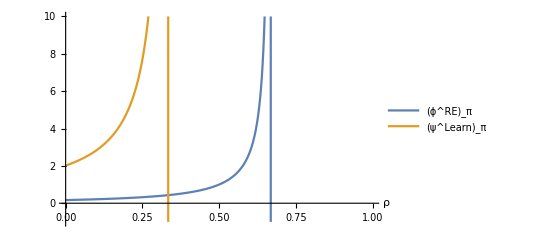

```mathematica
Plot[{REmatlab/.{β -> 0.99, σ-> 1, κ-> 0.1683, α-> 0.5, Subscript[λ, i]-> 1}, psipiopt/.{β -> 0.99, σ-> 1, κ-> 0.1683, α-> 0.5, Subscript[λ, i]-> 1}},{ρ,0,1},AxesLabel->Automatic, PlotLegends -> {"(ϕ^RE)_π", "(ψ^Learn)_π"}, PlotRange->{-1, 10}]
```

```mathematica
Export["/Users/lauragati/Dropbox/BC_Research/next/figures/materials15_opt_coeffs.pdf",%]
```

/Users/lauragati/Dropbox/BC_Research/next/figures/materials15_opt_coeffs.pdf

```mathematica
Manipulate[Plot[REmatlab/.{β -> 0.99, σ-> 1, κ-> 0.1683, α-> 0.5, Subscript[λ, i]-> m*1}, {ρ,0.01,1}], {m,0.01,1}]
```

```mathematica
Manipulate[Plot[psipiopt/.{β -> 0.99, σ-> 1, κ-> 0.1683, α-> 0.5, Subscript[λ, i]-> m*1}, {ρ,0.01,1}], {m,0.01,1}]
```

-> You can clearly see that all λ_i does is it scales the solution down: the bigger λ_i, the lower the optimal coefficient on inflation.